# Superposition discrète des ondes

(Impulsion périodique)

```mathematica
Clear["Global`*"]
```

## Impulsion périodique

La distribution spectrale des amplitudes:

```mathematica
A[k_]:=1/k
```

```mathematica
Table[A[k],{k,1,10,2}]
```

{1,1/3,1/5,1/7,1/9}

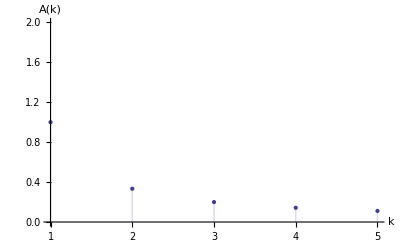

```mathematica
ListPlot[Table[A[k],{k,1,10,2}],Filling->Axis,PlotRange->{0,2},PlotStyle->Directive[PointSize[Large]],AxesLabel->{"k","A(k)"}]
```

Relation de dispersion :

```mathematica
ω[k_]:=4k
```

Fonction d’onde:

```mathematica
ψ[x_,t_]=Sum[A[k] ⅇ^(ⅈ (k x-ω[k] t)),{k,1,10,2}]
```

ⅇ^(ⅈ (-4 t+x))+1/3 ⅇ^(ⅈ (-12 t+3 x))+1/5 ⅇ^(ⅈ (-20 t+5 x))+1/7 ⅇ^(ⅈ (-28 t+7 x))+1/9 ⅇ^(ⅈ (-36 t+9 x))

```mathematica
Animate[Plot[Im[ψ[x,t]],{x,0,10},PlotRange->{-1,1},AxesLabel->{"t","Im[ψ(x,t)]"}],{t,0,2,0.01},AnimationRunning->False]
```

## Vitesse

Vitesse de phase (m/s)

```mathematica
Subscript[v, ϕ]=ω[k]/k
```

4

```mathematica
Table[Subscript[v, ϕ],{k,1,10}]
```

{4,4,4,4,4,4,4,4,4,4}

Vitesse de groupe (m/s)

```mathematica
Subscript[v, g]=D[ω[k],k]/.k->2
```

4